```mathematica
adjacencyMat = {{0,1,0,1},{1,0,1,1},{0,1,0,0},{1,1,0,0}}
```

{{0,1,0,1},{1,0,1,1},{0,1,0,0},{1,1,0,0}}

```mathematica
adjacencyMat//TableForm
```

0 | 1 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 1 | 0 | 0

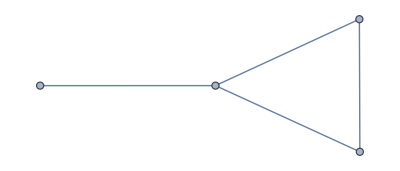

```mathematica
AdjacencyGraph[adjacencyMat]
```

```mathematica
adjacencyMat2 = {{1,1,0,1},{1,1,1,1},{0,1,1,0},{1,1,0,1}}
```

{{1,1,0,1},{1,1,1,1},{0,1,1,0},{1,1,0,1}}

```mathematica
adjacencyMat2//TableForm
```

1 | 1 | 0 | 1
1 | 1 | 1 | 1
0 | 1 | 1 | 0
1 | 1 | 0 | 1

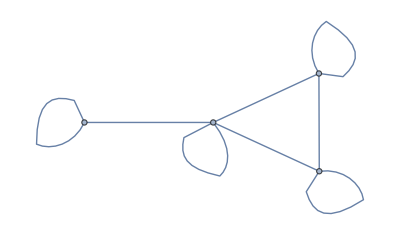

```mathematica
AdjacencyGraph[adjacencyMat2]
```

```mathematica
adjacencyMat3 = {{0,1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{0,0,0,1,0,0,0,0,1,1},{0,0,1,0,1,1,1,0,0,1},{0,0,0,1,0,0,1,0,0,1},{0,0,0,1,0,0,1,1,0,1},{0,1,0,1,1,1,0,1,0,1},{0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,0,1,0}}
```

```mathematica
{{0,1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{0,0,0,1,0,0,0,0,1,1},{0,0,1,0,1,1,1,0,0,1},{0,0,0,1,0,0,1,0,0,1},{0,0,0,1,0,0,1,1,0,1},{0,1,0,1,1,1,0,1,0,1},{0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,0,1,0}}
```

{{0,1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{0,0,0,1,0,0,0,0,1,1},{0,0,1,0,1,1,1,0,0,1},{0,0,0,1,0,0,1,0,0,1},{0,0,0,1,0,0,1,1,0,1},{0,1,0,1,1,1,0,1,0,1},{0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,0,1,0}}

```mathematica
adjacencyMat3//TableForm
```

0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0

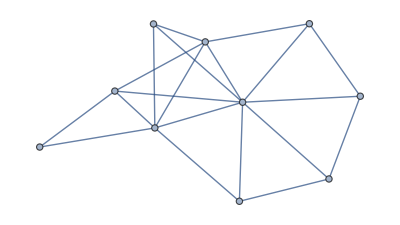

```mathematica
AdjacencyGraph[adjacencyMat3]
```

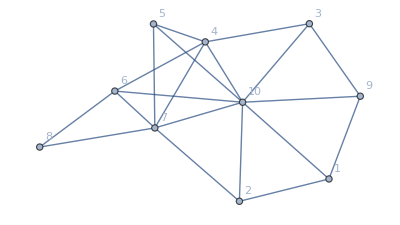

```mathematica
AdjacencyGraph[adjacencyMat3,VertexLabels->"Name"]
```